```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->14, Black}];
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->14,Black},LabelStyle->Black];
```

```mathematica
r0 = Entity["Particle","Electron"][EntityProperty["Particle","ClassicalRadius"]];
```

```mathematica
m0 = Entity["Particle","Electron"][EntityProperty["Particle","Mass"]];
```

```mathematica
c = Quantity[, "SpeedOfLight"];
```

```mathematica
En = Quantity[0.6673, "Megaelectronvolts"];
```

```mathematica
Ene[θ_]:= En-((En*m0*c^2)/(m0*c^2+En*(1-Cos[θ])))
```

```mathematica
Enp[θ_]:=En-Ene[θ]
```

```mathematica
g[θ_] := 1/2(Enp[θ]/En)^2(Enp[θ]/En+En/Enp[θ]-Sin[θ]^2)
```

```mathematica
dsEne[θ_]:=(2π r0^2 Sin[θ] g[θ])(((1+En/(m0*c^2)*(1-Cos[θ]))^2*m0*c^2)/(En^2*Sin[θ]))
```

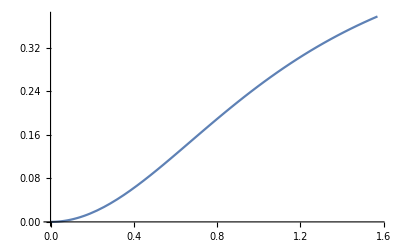

```mathematica
Plot[Ene[θ],{θ,0,Pi/2}]
```

```mathematica
Table[Ene[θ],{θ,0,π}]
```

{0. MeV,0.250318 MeV,0.433103 MeV,0.481871 MeV}

```mathematica
Table[Enp[θ],{θ,0,π}]
```

{0.6673 MeV,0.416982 MeV,0.234197 MeV,0.185429 MeV}

```mathematica
Table[g[θ],{θ,0,π}]
```

{1.,0.296198,0.146174,0.1489}

```mathematica
Table[UnitConvert[dsEne[θ],Quantity[, ("Centimeters")^2/("Megaelectronvolts")]],{θ,0.001,π}]
```

{5.7256×10^-25 cm^2/MeV,4.34251×10^-25 cm^2/MeV,6.79986×10^-25 cm^2/MeV,1.10421×10^-24 cm^2/MeV}

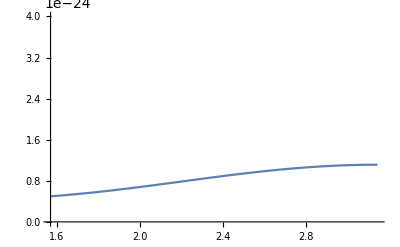

```mathematica
Plot[UnitConvert[dsEne[θ],Quantity[, ("Centimeters")^2/("Megaelectronvolts")]],{θ,π/2,π},PlotRange->{Full,{0,4*10^-24}}]
```

```mathematica
mixedpoints = Table[{Ene[θ],UnitConvert[dsEne[θ],Quantity[, ("Centimeters")^2/("Megaelectronvolts")]]},{θ,π/2,π,0.01}];
```

```mathematica
maxscatteredenergy =QuantityMagnitude[Max[mixedpoints[[All,1]]]]
```

0.482542

```mathematica
maxcrosssection = QuantityMagnitude[Max[mixedpoints[[All,2]]]]
```

1.11323×10^-24

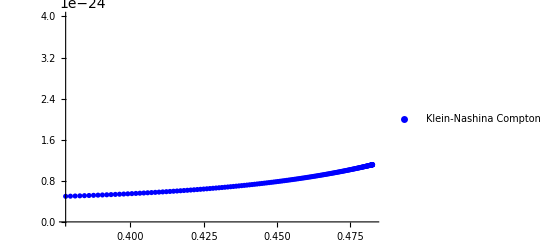

```mathematica
lplot =ListPlot[mixedpoints,PlotRange->{Full,{0,4*10^-24}},PlotLegends->Placed[LineLegend[{"Klein-Nashina Compton Scattering Distribution"}],Bottom],PlotStyle->{Blue},LabelStyle->Black,PlotRangePadding->0]
```

```mathematica
twodpoly = a1*x^2+b1*x+c1;
```

```mathematica
fitparams=FindFit[QuantityMagnitude[mixedpoints],twodpoly,{a1,b1,c1},x]
```

{a1→5.64698×10^-23,b1→-4.30351×10^-23,c1→8.72106×10^-24}

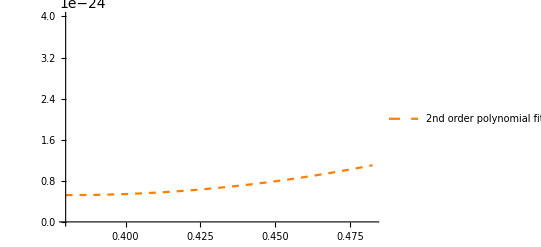

```mathematica
fplot = Plot[ a1*x^2+b1*x+c1/.fitparams,{x,0.38,maxscatteredenergy},PlotRange->{Full,{0,4*10^-24}},PlotStyle->{Orange, Dashed},PlotLegends->Placed[LineLegend[{"2nd order polynomial fit"}],Bottom],LabelStyle->Black,PlotRangePadding->0]
```

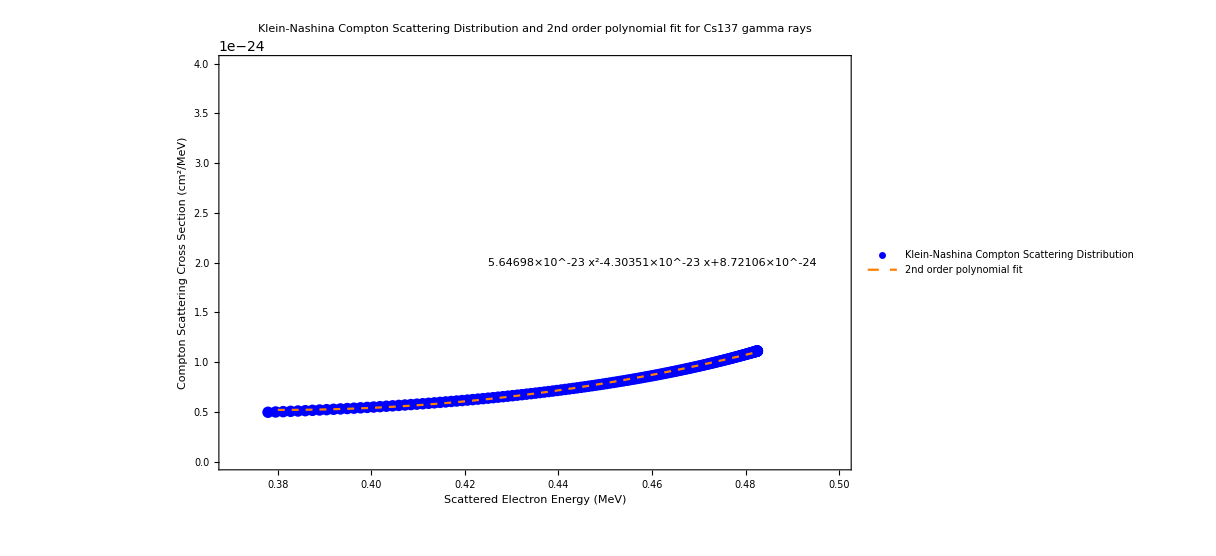

```mathematica
Show[lplot,fplot,PlotRange->{{0.37,0.5},{0,4*10^-24}},Frame->{True,True,False,False},FrameLabel->{"Scattered Electron Energy (MeV)","Compton Scattering Cross Section (cm^2/MeV)"},Axes->False,PlotLabel->Pane["Klein-Nashina Compton Scattering Distribution and 2nd order polynomial fit for Cs137 gamma rays",Alignment->Center],ImageSize->900,Epilog->{Style[Text[a1*x^2+b1*x+c1/.fitparams,{0.46,2*10^-24}],14]}]
```

```mathematica
pcwCompton[x_] := Piecewise[{{a1*x^2+b1*x+c1/.fitparams, x<=maxscatteredenergy},{0,x>maxscatteredenergy}}]
```

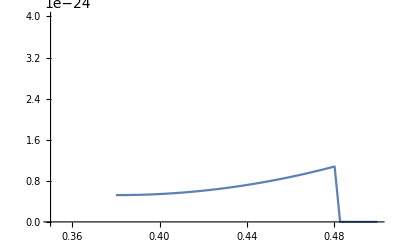

```mathematica
Plot[pcwCompton[x],{x,0.38,0.5},PlotRange->{{0.35,0.5},{0,4*10^-24}},Exclusions->None]
```

```mathematica
usCompton[x_]:=(a1*x^2+b1*x+c1/.fitparams )*(-UnitStep[x-maxscatteredenergy]+1)
```

```mathematica
Plot[usCompton[x],{x,0.38,0.5},PlotRange->{{0.35,0.5},{0,4*10^-24}},Exclusions->None]
```

-Graphics-